# Function Signature Rigour

## Tyson Jones tyson.jones@monash.edu July 2017

```mathematica
Clear["Global`*"]
```

## Description

To plot a wavefunction, you need its spatial form (number, list, function, symbolic expression AND symbols) in 1D or 2D, its numerical domain, its potential (number, list, function, symbolic expression IF symbols). To simulate a wavefunction, only additionally duration is needed

Possible formats

```mathematica
f[ (num | func | list),    { (symb)?,  num, num },     { (symb)?,  num, num }?,   Potential -> (num|func|list)?]
f[ symb,    { symb,  num, num },     { symb,  num, num }?,   Potential -> (num|func|list|symb)?]
f[ (num | func | list | symb),    { symb,  num, num },     { symb,  num, num }?,   Potential -> (symb)?]
```

That is, if either of the wavefunction of potential is symbolic (the other need not be), symbols MUST be passed in the domain (duh). If symbols are not passed in the domain, neither wavefunction nor potential may be symbolic

```mathematica
(* passing along optionvals to plot: 
https://stackoverflow.com/questions/8540947/problems-passing-options-in-specialized-plot-functions-for-mathematica
https://mathematica.stackexchange.com/questions/353/functions-with-options *)
```

```mathematica
(* args to function in arbitrary order http://reference.wolfram.com/language/ref/OrderlessPatternSequence.html *)
```

```mathematica
(* test whether symbol appears in expression: https://mathematica.stackexchange.com/questions/9772/determine-whether-some-expression-contains-a-given-symbol *)
```

```mathematica
(* test whether list/matrix contains numerics: https://mathematica.stackexchange.com/questions/16694/numericq-equivalent-for-lists *)
```

# 1D & 2D

## Definitions

```mathematica
Clear[finner]

Options[finner] = {
	TESTOPTION -> 2
};


(* 1D *)
finner[
	wavef:(_Function|_InterpolatingFunction),
	potential:(_Function|_InterpolatingFunction|None),
	{xL_?NumericQ, xR_?NumericQ},
	options:OptionsPattern[{finner, Plot}]
] := 
	With[
		{dummyvar = Evaluate @ FilterRules[{options, Options[finner]}, Options[Plot]]},
		True
	]
	
	
(* 2D *)
finner[
	wavef:(_Function|_InterpolatingFunction),
	potential:(_Function|_InterpolatingFunction|None),
	{xL_?NumericQ, xR_?NumericQ},
	{yL_?NumericQ, yR_?NumericQ},
	options:OptionsPattern[{finner, Plot}]
] := 
	With[
		{dummyvar = Evaluate @ FilterRules[{options, Options[finner]}, Options[Plot3D]]},
		"2D True"
	]
```

```mathematica
Clear[convertToFunc]

(* converts lists, constants and symbolic expressions to functions, leaving None unchanged *)


(* 1D *)
convertToFunc[None, ___] :=
	None
convertToFunc[const_?NumericQ, ___] :=
	(const &)
convertToFunc[func:(_Function|_InterpolatingFunction), ___] :=
	func
convertToFunc[list:_?(VectorQ[#, NumericQ]&), {___Symbol, xL_?NumericQ, xR_?NumericQ}] :=
	ListInterpolation[list, {{xL, xR}}]
convertToFunc[symbolic_, {symb_Symbol, ___}] :=
	Function @@ {symb, symbolic}
	
	
(* 2D *)
convertToFunc[
	matrix:_?(MatrixQ[#, NumericQ]&), 
	{___Symbol, xL_?NumericQ, xR_?NumericQ},
	{___Symbol, yL_?NumericQ, yR_?NumericQ}
] :=
	ListInterpolation[matrix, {{xL, xR}, {yL, yR}}]
	
convertToFunc[symbolic_, {symb1_Symbol, ___}, {symb2_Symbol, ___}] :=
	Function @@ {{symb1, symb2}, symbolic}
```

```mathematica
(* YOU CANNOT MIX 2D AND 3D PLOTTING *)
```

Show::gcomb: Could not combine the graphics objects in ….

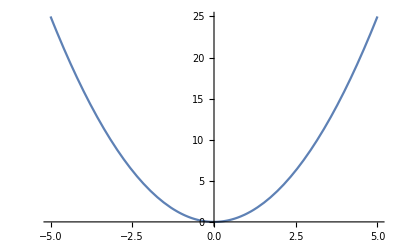
Show[-Graphics3D-,-Graphics-]

```mathematica
Show[
	Plot3D[ Exp[-x^2-y^2], {x, -5, 5}, {y, -1, 1} ],
	Plot[x^2, {x, -5, 5}]
]
```

```mathematica
Clear[validFunction]

(* 1D *)

(*
valid inputs are 
- a quantity
- a list of quantities (to be interpolated)
- a single-var function that evaluate to a quantity at end-points or middle of the domain
- an expression and symbol which evaluate to a quantity at end-points or middle of the domain
*)

validFunction[___] := 
	False
validFunction[_?NumericQ, ___] := 
	True
validFunction[list_/;VectorQ[list, NumericQ], ___] := 
	True
validFunction[func:(_Function|_InterpolatingFunction), {___Symbol, xL_?NumericQ, xR_?NumericQ}] :=
	NumericQ @ Quiet @ Check[func[xL], None] ||
	NumericQ @ Quiet @ Check[func[xR], None] ||
	NumericQ @ Quiet @ Check[func[(xL + xR)/2], None]
validFunction[symb_, {x_Symbol, xL_?NumericQ, xR_?NumericQ}] :=
	NumericQ[symb /. x -> xL] ||     
	NumericQ[symb /. x -> xR] ||
	NumericQ[symb /. x -> (xL + xR)/2]
```

```mathematica
(* I think Plot will actually match anything; maybe I should attempt to match anything, provided a var is passed? *)
```

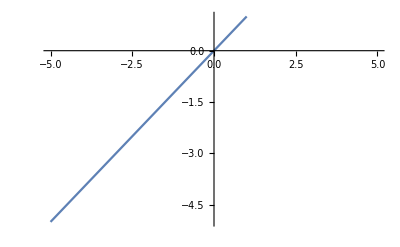

```mathematica
Plot[x + undefinedvar UnitStep[x-1], {x, -5, 5}]
```

should work

```mathematica
validFunction[4]
validFunction[{1, 2, 3, 4, 5}]
validFunction[(#&), {-5, 5}]
validFunction[(#&), {x, -5, 5}]
validFunction[x, {x, -5, 5}]
```

True

True

True

«2 more identical outputs»

should fail

```mathematica
validFunction[x]
validFunction[{1, 2, c, 4, 5}]
validFunction[(#1 + #2&), {-5, 5}]
validFunction[(#1 + #2&), {x, -5, 5}]
validFunction[(c #1 + #2&), {x, -5, 5}]
validFunction[x, {d, -5, 5}]
validFunction[#1 + poop &, {x, -5, 5}]
validFunction[#1 + x &, {x, -5, 5}]
```

False

False

False

«5 more identical outputs»

should but DON’T fail because of 0 factor killing unknown symbols

```mathematica
validFunction[d x, {d, -5, 5}]
validFunction[(c #&), {-5, 5}]
validFunction[(c #&), {x, -5, 5}]
```

True

True

True

```mathematica
Clear[fouter]
Clear[validOptions]

(* valid options (potential is valid input, if present) *)
validOptions[options:OptionsPattern[fouter], domain:{_?NumericQ, _?NumericQ}] := 
	Not[MemberQ[{options}, Potential -> _]] || 
	MemberQ[{options}, Potential -> v_ /; validFunction[v, domain]] 
	
validOptions[options:OptionsPattern[fouter], domain:{_Symbol, xL_?NumericQ, xR_?NumericQ}] := 
	validOptions[options, {xL, xR}] || 
	MemberQ[{options}, Potential -> v_ /; validFunction[v, domain]]


(* a symbolic wavefunction or potential requires explicit symbol parsing *)
Options[fouter] = {
	Potential -> None
};

fouter[
	wavef:_,
	domain:{___Symbol, xL_?NumericQ, xR_?NumericQ}, 
	options:OptionsPattern[{fouter, finner, Plot}]
] /; (
	validFunction[wavef, domain] && 
	validOptions[options, domain]
) :=
	finner[
		convertToFunc[wavef, domain],
		convertToFunc[OptionValue[Potential], domain],
		{xL, xR},
		Evaluate @ FilterRules[{options, Options[fouter]}, {Options[finner], Options[Plot]}]
	]
	

fouter[___] :=
	False
```

## Tests

should pass

```mathematica
fouter[(#&), {-5, 5}]
fouter[(#&), {-5, 5}, Potential -> {1, 2, 3, 4, 5}]
fouter[5, {-5, 5}]
fouter[x, {x, -5, 5}]
fouter[x, {x, -5, 5}, Potential -> (#&)]
fouter[x, {x, -5, 5}, Potential -> x]
fouter[(#&), {x, -5, 5}, Potential -> x]
fouter[{-5, -3, -1, 1, 3, 5}, { -5, 5}, Potential -> (#&)]
fouter[{-5, -3, -1, 1, 3, 5}, {x, -5, 5}, Potential -> x]
fouter[5, {x, -5, 5}, Potential -> x]
fouter[5, {x, -5, 5}, Potential ->Log[x+1]Sin[x]/Cos[x]]
fouter[(#&), {-5, 5}, PlotRange -> {0,2}]
fouter[(#&), {-5, 5},TESTOPTION-> {0,2}]
```

True

True

True

«10 more identical outputs»

should fail

```mathematica
fouter[( # + c&), {-5, 5}]
fouter[c(#&), {x, -5, 5}]
fouter[(#1 + #2 &), {-5, 5}]
fouter[d (#1 + #2 &), {-5, 5}]
fouter[(#1 + d #2 &), {-5, 5}]
fouter[(#1 + d #2 &), {d, -5, 5}]
fouter[(# &), {-5, 5}, Potential -> (#1 + #2 &)]
fouter[None, {-5, 5}]
fouter[None, {z, -5, 5}]
fouter[x, {a, -5, 5}]
fouter[x, {x, -5, 5}, Potential -> y]
fouter[(#&), {x, -5, 5}, Potential -> y]
fouter[x, {x, -5, 5}, Potential -> {a, b, c, d, e}]
fouter[{a, b, c, d, e}, {-5, 5}]
fouter[(#&), {-5, 5}, Potential -> {a, b, c, d, e}]
fouter[None, {-5, 5}]
fouter[(#&), {-a, b}]
fouter[x, {x, -a, 5}]
fouter[x, {a, -5, b}]
fouter[(#&), {-5, 5}, Potential -> x]
fouter[x, {x, y,  -5, 5}, Potential -> x]
fouter[x, {a,  -5, 5}, Potential -> x]
```

False

False

False

«19 more identical outputs»

should but DON’T fail because of 0 factor killing unknown symbols

```mathematica
fouter[(c #&), {-5, 5}]
fouter[(c #&), {x, -5, 5}]
fouter[(x #&), {x, -5, 5}]
fouter[x( #&), {x, -5, 5}]
fouter[( #&), { -5, 5}, Potential -> (c #&)]
```

True

True

True

«2 more identical outputs»

should error

```mathematica
fouter[(#&), {-5, 5},FALSEOPTION-> {0,2}]
```

OptionValue::nodef: Unknown option FALSEOPTION for {fouter,finner,Plot}.

True

ambiguous

```mathematica
fouter[(#&), {x, -5, 5}]
fouter[(#&), {x, -5, 5}, Potential -> (#&)]
fouter[{1, 2, 3, 4, 5}, {x, -5, 5}]
fouter[(#&), {x, -5, 5}, Potential -> {1, 2, 3, 4, 5}]
fouter[(#&), {-5, 5}, Potential -> None]
```

True

True

True

«1 more identical outputs»

False